```mathematica
(* Main params *)
Q=2000; (* 1100? *)
X=(Q^2+2)/4  ;

Timing[
(* get table, for each n of reps a^2+d^2=n, with 0≤ d<a *)
sumsqAll=Table[{},{j,1,X}];
sumsqHalf=Table[{},{j,1,X}];
For[a=1,a≤Sqrt[X/2],a++,
For[d=a+1,a^2+d^2≤X,d++,
AppendTo[sumsqAll[[a^2+d^2]],{a,d}];
AppendTo[sumsqAll[[a^2+d^2]],{d,a}];

AppendTo[sumsqAll[[a^2+d^2]],{a,-d}];
AppendTo[sumsqAll[[a^2+d^2]],{d,-a}];

AppendTo[sumsqAll[[a^2+d^2]],{-a,d}];
AppendTo[sumsqAll[[a^2+d^2]],{-d,a}];

AppendTo[sumsqAll[[a^2+d^2]],{-a,-d}];
AppendTo[sumsqAll[[a^2+d^2]],{-d,-a}];

AppendTo[sumsqHalf[[a^2+d^2]],{a,d}];
AppendTo[sumsqHalf[[a^2+d^2]],{d,a}];

AppendTo[sumsqHalf[[a^2+d^2]],{a,-d}];
AppendTo[sumsqHalf[[a^2+d^2]],{d,-a}];
];
];

(* diagonal *)
For[a=1,a≤Sqrt[X/2],a++,
AppendTo[sumsqAll[[2a^2]],{a,a}];
AppendTo[sumsqAll[[2a^2]],{a,-a}];
AppendTo[sumsqAll[[2a^2]],{-a,a}];
AppendTo[sumsqAll[[2a^2]],{-a,-a}];

AppendTo[sumsqHalf[[2a^2]],{a,a}];
AppendTo[sumsqHalf[[2a^2]],{a,-a}];

];

(* zeros *)
For[a=1,a≤Sqrt[X],a++,
AppendTo[sumsqAll[[a^2]],{0,a}];
AppendTo[sumsqAll[[a^2]],{0,-a}];
AppendTo[sumsqAll[[a^2]],{a,0}];
AppendTo[sumsqAll[[a^2]],{-a,0}];

AppendTo[sumsqHalf[[a^2]],{0,a}];
AppendTo[sumsqHalf[[a^2]],{a,0}];

];
]
sumsqHalf//Length
```

{15.9707,Null}

1000000

```mathematica
(* norm one elements of division algebra are a^2+d^2=1+3(b^2+c^2), or n=1+3m, with n, m sums of two squares  *)
prevTime=SessionTime[];
NumNormSqOv2s={}; (* how many mats are in Gamma with |g|^2 = j; store pairs {j, #} *)
angles={0,0}; (* set of all angles, starting with elliptic ones *)
For [m=1,m≤(Q^2-2)/12,m++,
adS=sumsqHalf[[1+3m]]; (* write n=1+3m as sum of squares in as many ways as possible *)
bcS=sumsqAll[[m]]; (* write m as sum of squares in as many ways as possible (maybe none) *)

If[Length[adS]Length[bcS]>0,
AppendTo[NumNormSqOv2s,{1+6m,Length[adS]Length[bcS]}]; (* number of such norms is product *)

For[j=1,j≤Length[bcS],j++,
For[k=1,k≤Length[adS],k++,

AppendTo[angles,
N[Arg[
(adS[[k,1]]bcS[[j,1]]+bcS[[j,2]]adS[[k,2]])
+I(adS[[k,1]]bcS[[j,2]]-bcS[[j,1]]adS[[k,2]])
]
]
];
];
];
];

If[Mod[m,1000]==0,
Print["Done with m=",m," out of ",Floor[(Q^2-2)/12], ". Number of secs used =",SessionTime[]-prevTime];
prevTime=SessionTime[];
];

];
angles=Sort[angles]/(2Pi);
tot=Length[angles]
```

Done with m=1000 out of 333333. Number of secs used =0.15212

Done with m=2000 out of 333333. Number of secs used =0.31882

Done with m=3000 out of 333333. Number of secs used =0.45329

Done with m=4000 out of 333333. Number of secs used =0.62907

Done with m=5000 out of 333333. Number of secs used =0.742202

Done with m=6000 out of 333333. Number of secs used =0.886248

Done with m=7000 out of 333333. Number of secs used =1.09028

Done with m=8000 out of 333333. Number of secs used =1.31984

Done with m=9000 out of 333333. Number of secs used =1.49197

Done with m=10000 out of 333333. Number of secs used =1.64217

Done with m=11000 out of 333333. Number of secs used =2.01791

Done with m=12000 out of 333333. Number of secs used =1.64262

Done with m=13000 out of 333333. Number of secs used =2.27714

Done with m=14000 out of 333333. Number of secs used =2.48277

Done with m=15000 out of 333333. Number of secs used =2.53676

Done with m=16000 out of 333333. Number of secs used =2.68674

Done with m=17000 out of 333333. Number of secs used =3.33228

Done with m=18000 out of 333333. Number of secs used =3.16614

Done with m=19000 out of 333333. Number of secs used =3.72181

Done with m=20000 out of 333333. Number of secs used =4.1022

Done with m=21000 out of 333333. Number of secs used =4.43484

Done with m=22000 out of 333333. Number of secs used =5.09951

Done with m=23000 out of 333333. Number of secs used =5.85006

Done with m=24000 out of 333333. Number of secs used =4.85161

Done with m=25000 out of 333333. Number of secs used =5.54276

Done with m=26000 out of 333333. Number of secs used =6.35432

Done with m=27000 out of 333333. Number of secs used =6.61666

Done with m=28000 out of 333333. Number of secs used =6.56296

Done with m=29000 out of 333333. Number of secs used =8.108472

Done with m=30000 out of 333333. Number of secs used =7.153531

Done with m=31000 out of 333333. Number of secs used =7.806767

Done with m=32000 out of 333333. Number of secs used =9.181032

Done with m=33000 out of 333333. Number of secs used =10.37957

Done with m=34000 out of 333333. Number of secs used =9.175709

Done with m=35000 out of 333333. Number of secs used =9.996802

Done with m=36000 out of 333333. Number of secs used =10.8224

Done with m=37000 out of 333333. Number of secs used =10.17916

Done with m=38000 out of 333333. Number of secs used =9.915445

Done with m=39000 out of 333333. Number of secs used =11.98399

Done with m=40000 out of 333333. Number of secs used =12.40931

Done with m=41000 out of 333333. Number of secs used =12.1981

Done with m=42000 out of 333333. Number of secs used =10.02436

Done with m=43000 out of 333333. Number of secs used =10.99944

Done with m=44000 out of 333333. Number of secs used =13.54658

Done with m=45000 out of 333333. Number of secs used =15.06076

Done with m=46000 out of 333333. Number of secs used =13.7857

Done with m=47000 out of 333333. Number of secs used =13.37886

Done with m=48000 out of 333333. Number of secs used =12.03737

Done with m=49000 out of 333333. Number of secs used =15.98063

Done with m=50000 out of 333333. Number of secs used =14.34803

Done with m=51000 out of 333333. Number of secs used =15.02322

Done with m=52000 out of 333333. Number of secs used =16.54576

Done with m=53000 out of 333333. Number of secs used =15.90913

Done with m=54000 out of 333333. Number of secs used =16.81044

Done with m=55000 out of 333333. Number of secs used =17.4656

Done with m=56000 out of 333333. Number of secs used =15.00547

Done with m=57000 out of 333333. Number of secs used =17.23195

Done with m=58000 out of 333333. Number of secs used =17.28552

Done with m=59000 out of 333333. Number of secs used =16.70116

Done with m=60000 out of 333333. Number of secs used =18.32976

Done with m=61000 out of 333333. Number of secs used =16.91444

Done with m=62000 out of 333333. Number of secs used =20.6184

Done with m=63000 out of 333333. Number of secs used =19.47282

Done with m=64000 out of 333333. Number of secs used =17.44777

Done with m=65000 out of 333333. Number of secs used =18.76608

Done with m=66000 out of 333333. Number of secs used =21.02379

Done with m=67000 out of 333333. Number of secs used =26.36482

Done with m=68000 out of 333333. Number of secs used =19.56879

Done with m=69000 out of 333333. Number of secs used =21.78104

Done with m=70000 out of 333333. Number of secs used =25.13411

Done with m=71000 out of 333333. Number of secs used =22.05995

Done with m=72000 out of 333333. Number of secs used =19.37315

Done with m=73000 out of 333333. Number of secs used =26.39375

Done with m=74000 out of 333333. Number of secs used =23.69501

Done with m=75000 out of 333333. Number of secs used =21.77028

Done with m=76000 out of 333333. Number of secs used =24.73484

Done with m=77000 out of 333333. Number of secs used =27.34335

Done with m=78000 out of 333333. Number of secs used =26.33099

Done with m=79000 out of 333333. Number of secs used =23.7818

Done with m=80000 out of 333333. Number of secs used =25.62853

Done with m=81000 out of 333333. Number of secs used =23.85158

Done with m=82000 out of 333333. Number of secs used =27.16049

Done with m=83000 out of 333333. Number of secs used =21.93864

Done with m=84000 out of 333333. Number of secs used =21.7421

Done with m=85000 out of 333333. Number of secs used =27.16768

Done with m=86000 out of 333333. Number of secs used =27.19929

Done with m=87000 out of 333333. Number of secs used =29.63928

Done with m=88000 out of 333333. Number of secs used =22.55862

Done with m=89000 out of 333333. Number of secs used =30.37092

Done with m=90000 out of 333333. Number of secs used =31.65395

Done with m=91000 out of 333333. Number of secs used =33.31342

Done with m=92000 out of 333333. Number of secs used =34.47375

Done with m=93000 out of 333333. Number of secs used =29.7324

Done with m=94000 out of 333333. Number of secs used =36.69024

Done with m=95000 out of 333333. Number of secs used =35.94233

Done with m=96000 out of 333333. Number of secs used =23.44579

Done with m=97000 out of 333333. Number of secs used =28.6735

Done with m=98000 out of 333333. Number of secs used =36.31568

Done with m=99000 out of 333333. Number of secs used =36.65519

Done with m=100000 out of 333333. Number of secs used =31.41249

Done with m=101000 out of 333333. Number of secs used =30.60936

Done with m=102000 out of 333333. Number of secs used =34.66463

Done with m=103000 out of 333333. Number of secs used =28.00846

Done with m=104000 out of 333333. Number of secs used =36.49158

Done with m=105000 out of 333333. Number of secs used =30.10611

Done with m=106000 out of 333333. Number of secs used =36.74064

Done with m=107000 out of 333333. Number of secs used =36.069

Done with m=108000 out of 333333. Number of secs used =32.4265

Done with m=109000 out of 333333. Number of secs used =35.74267

Done with m=110000 out of 333333. Number of secs used =24.4931

Done with m=111000 out of 333333. Number of secs used =40.11392

Done with m=112000 out of 333333. Number of secs used =39.25128

Done with m=113000 out of 333333. Number of secs used =36.42026

Done with m=114000 out of 333333. Number of secs used =41.24149

Done with m=115000 out of 333333. Number of secs used =149.39206

Done with m=116000 out of 333333. Number of secs used =36.66151

Done with m=117000 out of 333333. Number of secs used =35.63084

Done with m=118000 out of 333333. Number of secs used =38.81852

Done with m=119000 out of 333333. Number of secs used =40.67153

Done with m=120000 out of 333333. Number of secs used =37.36588

Done with m=121000 out of 333333. Number of secs used =38.94074

Done with m=122000 out of 333333. Number of secs used =47.38214

Done with m=123000 out of 333333. Number of secs used =41.99593

Done with m=124000 out of 333333. Number of secs used =40.12668

Done with m=125000 out of 333333. Number of secs used =34.46949

Done with m=126000 out of 333333. Number of secs used =44.08273

Done with m=127000 out of 333333. Number of secs used =40.50762

Done with m=128000 out of 333333. Number of secs used =38.78874

Done with m=129000 out of 333333. Number of secs used =42.02991

Done with m=130000 out of 333333. Number of secs used =40.22038

Done with m=131000 out of 333333. Number of secs used =45.47459

Done with m=132000 out of 333333. Number of secs used =53.92069

Done with m=133000 out of 333333. Number of secs used =40.44693

Done with m=134000 out of 333333. Number of secs used =38.96784

Done with m=135000 out of 333333. Number of secs used =45.06759

Done with m=136000 out of 333333. Number of secs used =41.6244

Done with m=137000 out of 333333. Number of secs used =39.08703

Done with m=138000 out of 333333. Number of secs used =42.61274

Done with m=139000 out of 333333. Number of secs used =47.67814

Done with m=140000 out of 333333. Number of secs used =46.34682

Done with m=141000 out of 333333. Number of secs used =46.04361

Done with m=142000 out of 333333. Number of secs used =40.57259

Done with m=143000 out of 333333. Number of secs used =51.2459

Done with m=144000 out of 333333. Number of secs used =49.79405

Done with m=145000 out of 333333. Number of secs used =36.71136

Done with m=146000 out of 333333. Number of secs used =51.07746

Done with m=147000 out of 333333. Number of secs used =44.26375

Done with m=148000 out of 333333. Number of secs used =48.4789

Done with m=149000 out of 333333. Number of secs used =44.29082

Done with m=150000 out of 333333. Number of secs used =50.71558

Done with m=151000 out of 333333. Number of secs used =52.40888

Done with m=152000 out of 333333. Number of secs used =40.15569

Done with m=153000 out of 333333. Number of secs used =55.45938

Done with m=154000 out of 333333. Number of secs used =47.10183

Done with m=155000 out of 333333. Number of secs used =57.3122

Done with m=156000 out of 333333. Number of secs used =51.72016

Done with m=157000 out of 333333. Number of secs used =42.7846

Done with m=158000 out of 333333. Number of secs used =52.73544

Done with m=159000 out of 333333. Number of secs used =46.28427

Done with m=160000 out of 333333. Number of secs used =53.60948

Done with m=161000 out of 333333. Number of secs used =49.39881

Done with m=162000 out of 333333. Number of secs used =50.51055

Done with m=163000 out of 333333. Number of secs used =53.83953

Done with m=164000 out of 333333. Number of secs used =66.38564

Done with m=165000 out of 333333. Number of secs used =53.58203

Done with m=166000 out of 333333. Number of secs used =45.72754

Done with m=167000 out of 333333. Number of secs used =57.56152

Done with m=168000 out of 333333. Number of secs used =54.68402

Done with m=169000 out of 333333. Number of secs used =47.15856

Done with m=170000 out of 333333. Number of secs used =46.51556

Done with m=171000 out of 333333. Number of secs used =57.78713

Done with m=172000 out of 333333. Number of secs used =50.62755

Done with m=173000 out of 333333. Number of secs used =50.60068

Done with m=174000 out of 333333. Number of secs used =58.46564

Done with m=175000 out of 333333. Number of secs used =56.68789

Done with m=176000 out of 333333. Number of secs used =64.22143

Done with m=177000 out of 333333. Number of secs used =50.52463

Done with m=178000 out of 333333. Number of secs used =55.41544

Done with m=179000 out of 333333. Number of secs used =64.4277

Done with m=180000 out of 333333. Number of secs used =61.62704

Done with m=181000 out of 333333. Number of secs used =62.153

Done with m=182000 out of 333333. Number of secs used =61.49688

Done with m=183000 out of 333333. Number of secs used =63.08628

Done with m=184000 out of 333333. Number of secs used =63.80983

Done with m=185000 out of 333333. Number of secs used =59.99445

Done with m=186000 out of 333333. Number of secs used =58.27827

Done with m=187000 out of 333333. Number of secs used =54.20763

Done with m=188000 out of 333333. Number of secs used =55.59692

Done with m=189000 out of 333333. Number of secs used =63.50817

Done with m=190000 out of 333333. Number of secs used =76.626994

Done with m=191000 out of 333333. Number of secs used =68.35598

Done with m=192000 out of 333333. Number of secs used =48.96349

Done with m=193000 out of 333333. Number of secs used =57.78529

Done with m=194000 out of 333333. Number of secs used =59.45529

Done with m=195000 out of 333333. Number of secs used =65.9244

Done with m=196000 out of 333333. Number of secs used =63.11194

Done with m=197000 out of 333333. Number of secs used =58.89905

Done with m=198000 out of 333333. Number of secs used =76.781211

Done with m=199000 out of 333333. Number of secs used =71.5945

Done with m=200000 out of 333333. Number of secs used =64.67405

Done with m=201000 out of 333333. Number of secs used =71.712074

Done with m=202000 out of 333333. Number of secs used =63.60557

Done with m=203000 out of 333333. Number of secs used =59.69224

Done with m=204000 out of 333333. Number of secs used =83.278525

Done with m=205000 out of 333333. Number of secs used =77.931714

Done with m=206000 out of 333333. Number of secs used =61.22625

Done with m=207000 out of 333333. Number of secs used =59.12553

Done with m=208000 out of 333333. Number of secs used =62.56037

Done with m=209000 out of 333333. Number of secs used =67.37873

Done with m=210000 out of 333333. Number of secs used =64.06422

Done with m=211000 out of 333333. Number of secs used =64.16871

Done with m=212000 out of 333333. Number of secs used =69.18268

Done with m=213000 out of 333333. Number of secs used =68.05154

Done with m=214000 out of 333333. Number of secs used =57.88149

Done with m=215000 out of 333333. Number of secs used =59.72766

Done with m=216000 out of 333333. Number of secs used =69.99938

Done with m=217000 out of 333333. Number of secs used =65.52537

Done with m=218000 out of 333333. Number of secs used =77.878655

Done with m=219000 out of 333333. Number of secs used =69.24046

Done with m=220000 out of 333333. Number of secs used =72.608921

Done with m=221000 out of 333333. Number of secs used =75.936239

Done with m=222000 out of 333333. Number of secs used =63.95866

Done with m=223000 out of 333333. Number of secs used =72.771302

Done with m=224000 out of 333333. Number of secs used =81.639016

Done with m=225000 out of 333333. Number of secs used =65.56528

Done with m=226000 out of 333333. Number of secs used =72.304772

Done with m=227000 out of 333333. Number of secs used =70.21333

Done with m=228000 out of 333333. Number of secs used =57.1103

Done with m=229000 out of 333333. Number of secs used =76.739839

Done with m=230000 out of 333333. Number of secs used =77.691357

Done with m=231000 out of 333333. Number of secs used =79.176689

Done with m=232000 out of 333333. Number of secs used =73.087177

Done with m=233000 out of 333333. Number of secs used =74.279441

Done with m=234000 out of 333333. Number of secs used =71.335517

Done with m=235000 out of 333333. Number of secs used =83.474386

Done with m=236000 out of 333333. Number of secs used =82.257671

Done with m=237000 out of 333333. Number of secs used =82.452277

Done with m=238000 out of 333333. Number of secs used =82.508293

Done with m=239000 out of 333333. Number of secs used =74.364448

Done with m=240000 out of 333333. Number of secs used =86.662496

Done with m=241000 out of 333333. Number of secs used =78.181997

Done with m=242000 out of 333333. Number of secs used =67.64236

Done with m=243000 out of 333333. Number of secs used =78.921021

Done with m=244000 out of 333333. Number of secs used =80.427384

Done with m=245000 out of 333333. Number of secs used =77.283313

Done with m=246000 out of 333333. Number of secs used =64.81916

Done with m=247000 out of 333333. Number of secs used =76.64972

Done with m=248000 out of 333333. Number of secs used =84.293194

Done with m=249000 out of 333333. Number of secs used =96.856759

Done with m=250000 out of 333333. Number of secs used =66.5808

Done with m=251000 out of 333333. Number of secs used =93.221222

Done with m=252000 out of 333333. Number of secs used =54.0619

Done with m=253000 out of 333333. Number of secs used =108.90265

Done with m=254000 out of 333333. Number of secs used =77.063871

Done with m=255000 out of 333333. Number of secs used =85.846578

Done with m=256000 out of 333333. Number of secs used =81.61895

Done with m=257000 out of 333333. Number of secs used =97.824976

Done with m=258000 out of 333333. Number of secs used =84.335001

Done with m=259000 out of 333333. Number of secs used =100.2754

Done with m=260000 out of 333333. Number of secs used =82.352108

Done with m=261000 out of 333333. Number of secs used =96.644993

Done with m=262000 out of 333333. Number of secs used =75.804399

Done with m=263000 out of 333333. Number of secs used =87.34124

Done with m=264000 out of 333333. Number of secs used =82.885775

Done with m=265000 out of 333333. Number of secs used =97.742947

Done with m=266000 out of 333333. Number of secs used =78.751631

Done with m=267000 out of 333333. Number of secs used =85.39841

Done with m=268000 out of 333333. Number of secs used =78.231102

Done with m=269000 out of 333333. Number of secs used =72.231371

Done with m=270000 out of 333333. Number of secs used =72.321671

Done with m=271000 out of 333333. Number of secs used =97.827996

Done with m=272000 out of 333333. Number of secs used =86.979449

Done with m=273000 out of 333333. Number of secs used =95.297917

Done with m=274000 out of 333333. Number of secs used =99.917813

Done with m=275000 out of 333333. Number of secs used =73.178687

Done with m=276000 out of 333333. Number of secs used =89.327715

Done with m=277000 out of 333333. Number of secs used =86.216417

Done with m=278000 out of 333333. Number of secs used =83.623532

Done with m=279000 out of 333333. Number of secs used =89.85344

Done with m=280000 out of 333333. Number of secs used =102.49433

Done with m=281000 out of 333333. Number of secs used =95.628452

Done with m=282000 out of 333333. Number of secs used =87.073985

Done with m=283000 out of 333333. Number of secs used =90.023633

Done with m=284000 out of 333333. Number of secs used =98.072937

Done with m=285000 out of 333333. Number of secs used =97.887812

Done with m=286000 out of 333333. Number of secs used =112.8945

Done with m=287000 out of 333333. Number of secs used =93.894973

Done with m=288000 out of 333333. Number of secs used =89.21492

Done with m=289000 out of 333333. Number of secs used =100.81431

Done with m=290000 out of 333333. Number of secs used =86.748937

Done with m=291000 out of 333333. Number of secs used =94.271167

Done with m=292000 out of 333333. Number of secs used =99.991967

Done with m=293000 out of 333333. Number of secs used =103.49013

Done with m=294000 out of 333333. Number of secs used =89.669953

Done with m=295000 out of 333333. Number of secs used =91.637457

Done with m=296000 out of 333333. Number of secs used =115.12017

Done with m=297000 out of 333333. Number of secs used =97.615003

Done with m=298000 out of 333333. Number of secs used =108.15792

Done with m=299000 out of 333333. Number of secs used =107.29444

Done with m=300000 out of 333333. Number of secs used =70.927741

Done with m=301000 out of 333333. Number of secs used =115.0422

Done with m=302000 out of 333333. Number of secs used =81.240789

Done with m=303000 out of 333333. Number of secs used =98.12426

Done with m=304000 out of 333333. Number of secs used =102.62204

Done with m=305000 out of 333333. Number of secs used =111.05754

Done with m=306000 out of 333333. Number of secs used =103.35242

Done with m=307000 out of 333333. Number of secs used =88.952007

Done with m=308000 out of 333333. Number of secs used =112.52674

Done with m=309000 out of 333333. Number of secs used =97.618205

Done with m=310000 out of 333333. Number of secs used =100.66719

Done with m=311000 out of 333333. Number of secs used =102.18728

Done with m=312000 out of 333333. Number of secs used =109.18813

Done with m=313000 out of 333333. Number of secs used =115.0193

Done with m=314000 out of 333333. Number of secs used =85.09515

Done with m=315000 out of 333333. Number of secs used =92.412224

Done with m=316000 out of 333333. Number of secs used =127.93581

Done with m=317000 out of 333333. Number of secs used =127.91376

Done with m=318000 out of 333333. Number of secs used =93.356724

Done with m=319000 out of 333333. Number of secs used =101.46675

Done with m=320000 out of 333333. Number of secs used =94.603128

Done with m=321000 out of 333333. Number of secs used =102.13925

Done with m=322000 out of 333333. Number of secs used =97.670885

Done with m=323000 out of 333333. Number of secs used =86.081346

Done with m=324000 out of 333333. Number of secs used =88.318958

Done with m=325000 out of 333333. Number of secs used =121.39996

Done with m=326000 out of 333333. Number of secs used =92.804298

Done with m=327000 out of 333333. Number of secs used =100.88587

Done with m=328000 out of 333333. Number of secs used =99.154993

Done with m=329000 out of 333333. Number of secs used =110.70771

Done with m=330000 out of 333333. Number of secs used =115.91631

Done with m=331000 out of 333333. Number of secs used =89.106518

Done with m=332000 out of 333333. Number of secs used =116.92216

Done with m=333000 out of 333333. Number of secs used =113.71812

2000914

```mathematica
vep=0.005;
maxXi=5;
```

```mathematica
(* First  the theoretical pic *) 
f[ell_,xi_]:=2/xi^2 Piecewise[{
{Log[(Cosh[ell]+Sinh[ell])/(Cosh[ell]+Sqrt[Sinh[ell]^2-xi^2])],
xi≤2Sinh[ell/2]
}
,
{Log[(Cosh[ell]+Sinh[ell])(1+xi^2)/(Cosh[ell]+Sqrt[Sinh[ell]^2-xi^2])^2],
2Sinh[ell/2]<=xi<=Sinh[ell]
}
,
{ell,
Sinh[ell]<=xi
}
}
];
```

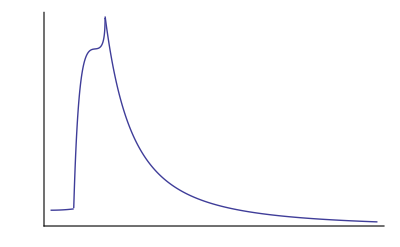

```mathematica
Plot[ f[3,xi 6],{xi,0.001,10},PlotRange->All,AxesOrigin->{0,0},PlotPoints->320,PlotStyle->Thick,Ticks->False]
```

```mathematica
Vgam=Pi Q^2/tot//N
g2[xi_]:=Vgam /(2Pi)Sum[NumNormSqOv2s[[i,2]] f[N[ArcCosh[NumNormSqOv2s[[i,1]]]],xi Vgam],{i,1,Length[NumNormSqOv2s]}];

Timing[
g2ListTh=Table[{xi,g2[xi]},{xi,vep,maxXi,vep}];
]
```

5.02655

{0.02587,Null}

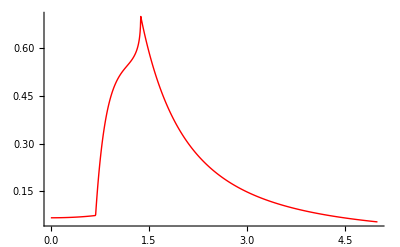

```mathematica
pic2=ListPlot[g2ListTh,Joined->True,PlotStyle->Directive[Red,Thick],PlotRange->{{0,maxXi},All}]
```

```mathematica
pic2=ListPlot[g2ListTh,Joined->True,PlotStyle->Directive[Red,Thick],PlotRange->{{0,maxXi},All}]
```

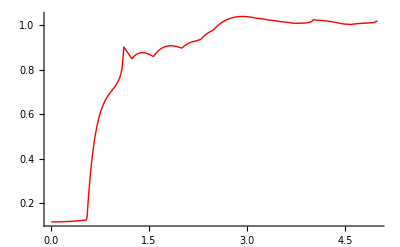
```mathematica
pic2=-Graphics-
```

-Graphics-

```mathematica
(* Now for the empirical pic *)
```

```mathematica
(* construct the g_2 function at a few sample points *)
Timing[
numCounts=Floor[maxXi/vep];
g2counts=ConstantArray[0,numCounts];
For[i=1,i<tot,i++,
For[j=i+1,j≤tot,j++,
k=Floor[tot/vep Abs[angles[[j]]-angles[[i]]  ]   ]+1;
If[k>numCounts,
j=tot+1; (* kick out *)
,
g2counts[[k]]++;
];
];
];
]
```

{64.3181,Null}

```mathematica
Save["g2List.m",g2List]
```

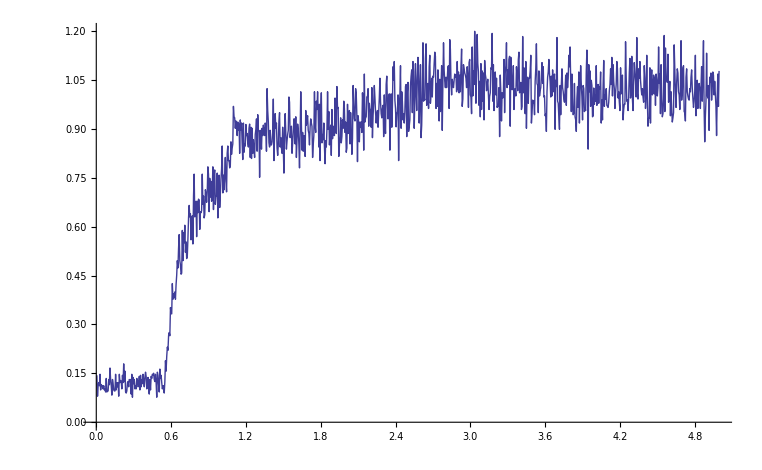

```mathematica
g2List=Table[{(k-1) vep,g2counts[[k]]/tot/vep},{k,2,numCounts}];
pic1=ListPlot[g2List,Joined->True]
```

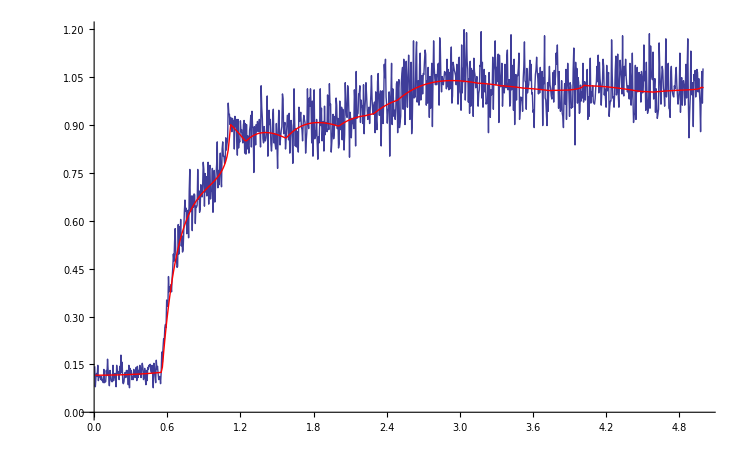

```mathematica
Show[pic1,pic2]
```

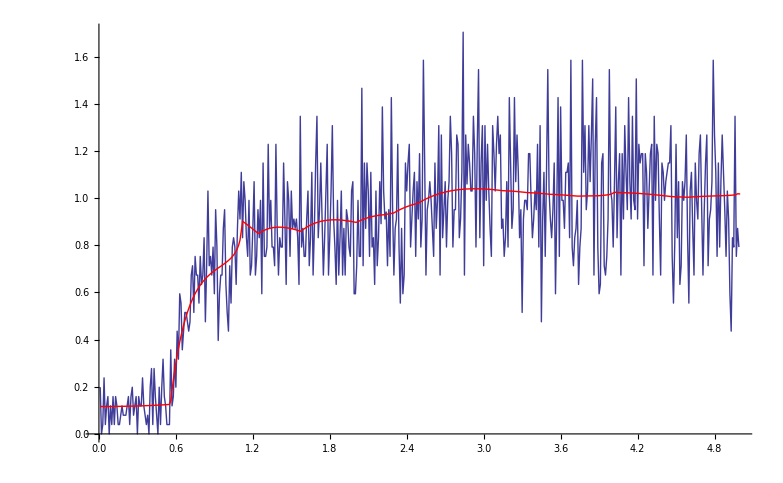

```mathematica
Show[pic1,pic2]
```